Name: Bella  Falbo

# Mathematica Tutorial 2 : Working with Lists and Tables

Adapted  by C. Golé, Smith College, from 
Introduction to Computational Science:  Modeling and Simulation for the Sciences
Angela B. Shiflet and George W. Shiflet
Wofford College
© 2006 by Princeton University Press Tutorial © 2009
Latest update: January 2024

## Introduction

The prerequisite to this tutorial is "Mathematica Tutorial 1."  The tutorial introduces the following functions and concepts: lists, ListPlot, Joined, comments, and Append.  Table is a powerful way to create a list, that can include an actual loop program. Execute all input cells to view the results of the examples, and perform the QRQ’s. When done, upload that to your google folder.

## 1. Lists

Many Mathematica applications involve lists, and a number of built-in functions perform operations on lists.  Braces, { }, enclose the values in a list, such as follows:

```mathematica
numList={13,36,92}
```

{13,36,92}

We also employ a list to store an ordered pair, such as the following representation of the point (-3, 46):

```mathematica
orderedPair={-3,46}
```

{-3,46}

#### QRQ (Quick Review Question) 1.1 As for the first tutorial, do anything that is asked of you in cells that look like this one, marked as a QRQ in boldface. Because such cells are text cells and not input cells, do not type in these cells. Instead, move the cursor down until it changes from being vertical to being a horizontal-I bar. Click and start typing; a new input cell will form. For this question, assign to ptLst a list representing the following ordered pairs (points): (-3, 6), (5, 2), and (1, 12).

```mathematica
ptLst = {{-3,6},{5,2}, {1,12}}
```

{{-3,6},{5,2},{1,12}}

The elements of a list have a numeric order (index) starting with 1, and we can refer to a particular element by using the name of the list and double square brackets, [[ ]],  surrounding that number.  For example, the second element of numList above is as follows:

```mathematica
numList[[2]]
```

36

Besides using a number, such as 2, we can employ a variable, such as i, that has a value, so that numList[[i]] refers to the i-th element of the list.  Consequently, a Do loop can process the elements of a list individually by having the varying loop index specify the list element.

#### QRQ 1.2 Using Print and a Do loop, print on separate lines the points of ptLst from QRQ 1.1.

```mathematica
Do[Print[ptLst[[i]]],{i,1,3}]
```

{-3,6}

{5,2}

{1,12}

Frequently, a list occurs within a list, such as the following list that represents a matrix with two rows, each in braces, and four columns:

```mathematica
mat = {{45, 99, 203, -29}, {775, 31, -582, 62}}
```

{{45,99,203,-29},{775,31,-582,62}}

The Classroom Assistant's Advanced Calculator provides an alternative method for establishing the matrix by clicking (□ | □
□ | □) and Ctrl [,] twice for two additional columns.  We tab from cell to cell while entering the matrices values.  The resulting input cell appears as follows:

```mathematica
mat = ({{45, 99, 203, -29}, {775, 31, -582, 62}})
```

{{45,99,203,-29},{775,31,-582,62}}

With mat having two elements, the rows, we reference the first row, {45, 99, 203, -29}, as follows:

```mathematica
mat[[1]][[3]]
```

203

Those who have taken linear algebra may remember: the order is always “row - column.” 
Alternatively, we employ the following notation that separates the indices with a comma:

```mathematica
mat[[1, 3]]
```

203

#### QRQ 1.3 Write commands using ptLst and double square brackets to return the following parts of ptLst from QRQ 1.1: a. The third point, (1, 12)

```mathematica
ptLst[[3]]
```

{1,12}

#### b. The first coordinate of the second point, 5. Use two pairs of double square brackets.

```mathematica
ptLst[[2]][[1]]
```

5

#### c. The first coordinate of the second point, 5. Use one pair of double square brackets.

```mathematica
ptLst[[2,1]]
```

5

#### d. The second coordinate of the first point, 6. Use two pairs of double square brackets.

```mathematica
ptLst[[1]][[2]]
```

6

#### e. The second coordinate of the first point, 6. Use one pair of double square brackets.

```mathematica
ptLst[[1,2]]
```

6

## 2. Graphing points and lists

To plot points in a list, we use ListPlot.  The segment below assigns a list of points to the variable pts and then displays the points with the appropriate axes labels by employing the option AxesLabel, which is also available for Plot.  In this example, two statements appear in one cell, the assignment of a list to pts and ListPlot.  As the following segment indicates, output for each command occurs after the input cell:

{{-3,2},{2,2},{-1,-1},{4,3},{0,0}}

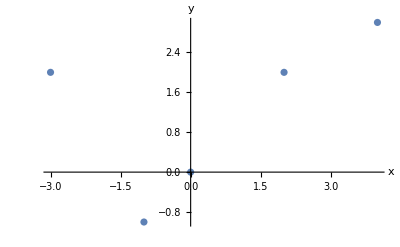

```mathematica
pts={{-3,2},{2,2},{-1,-1},{4,3},{0,0}}
ListPlot[pts,AxesLabel->{" x "," y "}]
```

To obtain the appropriate ListPlot template with Classroom Assistant, we select Basic Commands and 2D and then click ListPlot or More under Visualizing Data.  Afterwards, under Options, we select the appropriate AxesLabel template on the Axes & Frame drop-down menu.

```mathematica
ListPlot[{Subscript[y, 1],Subscript[y, 2],…},AxesLabel->{x label,y label}]
```

-Graphics-

#### QRQ 2.1 Using the Classroom Assistant, graph the points in list ptLst from the previous section. Have labeled axes.

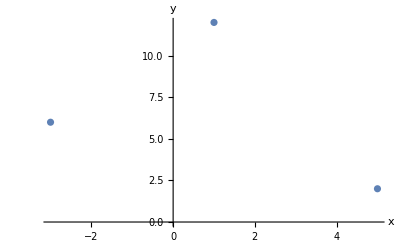

```mathematica
ListPlot[ptLst, AxesLabel->{"x","y"}]
```

In the command below, we make the points bigger and assign the graph to a variable, lp, for later reuse.  To have larger points, we employ the option PlotStyle with the directive PointSize, which indicates the diameter of points as a fraction of the graph's width.  Thus, the following command designates that the diameter of any point be 0.03 = 3% of the total width of the graphics:

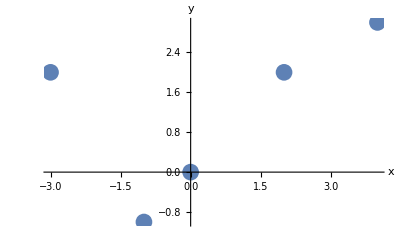

```mathematica
lp=ListPlot[pts,AxesLabel->{" x "," y "},PlotStyle->{PointSize[0.03]}]
```

A template for PlotStyle is available in under Classroom Assistant, Basic Commands, 2D, Options, Style.

#### QRQ 2.2 Copy to a new cell the answer of the previous QRQ to plot the list of points stored in variable ptLst. Adjust the command to have the points appear larger. What about red points? (Check Help for PlotStyle).

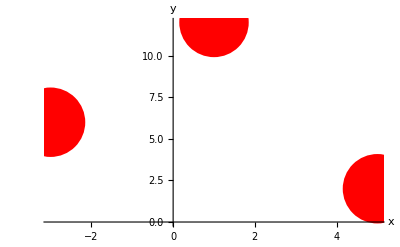

```mathematica
lpgraph=ListPlot[ptLst, AxesLabel->{"x","y"},PlotStyle->{PointSize[0.3],Red}]
```

## 3. Lines connecting points

Sometimes, it is helpful to visualize the path of an entity, such as an animal, a planet or a molecule, whose movement we are simulating.  To generate the path, we specify True for the ListPlot option Joined, as Joined ->True.  The subsequent graph displays line segments joining pairs of adjacent points.  (A template for Joined → True is available in under Classroom Assistant, Basic Commands, 2D, Options, Specific.)

For example, suppose {-1, 0, -1, 0, 1, 2, 3, 2, 1, 0} is a list (ylst) of y values, where each element is randomly one more or less than the previous element.  Considering each y value to occur at sequential ticks of the clock, we can draw a line graph to display the trend of the y values over time.  Just plotting ylst causes the first coordinates of the points to be 1, 2, ..., 10 and the corresponding second coordinates to be from ylst.  The segment display the trend of y over time follows:

```mathematica
ylst={-1,0,-1,0,1,2,3,2,1,0};
```

```mathematica
lp=ListPlot[ylst,AxesLabel->{"t","y"},Joined->True]
```

or:

```mathematica
lp=ListLinePlot[ylst,AxesLabel->{"t","y"}]
```

#### QRQ 3.1 Plot the list of points stored in variable ptLst from the QRQs of the first section (Lists). Label the axes, and connect the points with line segments.

Of course you can also join points given by their 2 coordinates. Here is an interesting example. See what each command outputs to learn about how lists can be created and manipulated. You will be ask to comment on what each line does in the next section.

{1,2,3,4}

{0,-1,0,1}

{1,0,-1,0}

{{0,-1,0,1},{1,0,-1,0}}

{{0,1},{-1,0},{0,-1},{1,0}}

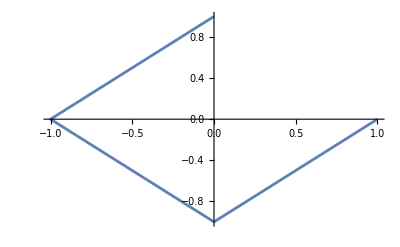

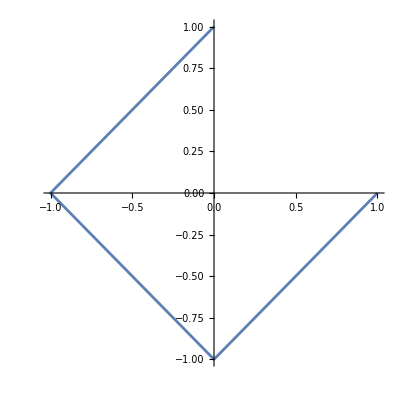

```mathematica
(* draft of a program to draw a square *)

tlist = Range[1,4]
xlist = Cos[π/2 tlist]
ylist = Sin[π/2 tlist]
notSoGoodSquarePts = {xlist, ylist}

squarepts = Transpose[{xlist, ylist}]

notSoSquare = ListLinePlot[squarepts]

almostFullSquare = ListLinePlot[squarepts, AspectRatio->Automatic]
```

## 4. Comments

Any program, regardless of the language, should have ample comments to explain the code.  It is amazingly easy to forget what you did only a few minutes earlier.  It takes far less time to enter the comments as we type the program than to figure out the code later.  A descriptive software engineering phrase is "Write once, read many times."  
	
We have been using Mathematica notebook cells with styles, such as Text, to record comments.  However, for longer segments of code, internal comments are also helpful.  In Mathematica, comments appear between (* and *), and the computer ignores text between this pair of delimiters.  Examples of comments follow:

```mathematica
(* A comment can appear on a line or lines by itself 
 or can document code on a line *)
lst = {};  (* initialize list to empty *)
```

#### QRQ 4.1 a. Write a statement to assign 80 to the variable v, and in a comment on the same line indicate that the variable represents "velocity in km/hr."

b. Copy the entire cell starting with (* draft of a program to draw a square *) in the section above, and comment each line of the program

c. Complete and clean up that program (removing unnecessary lines) so that it produces a full square (Hint. you may have to change the first command a bit)

Sometimes, we wish to temporarily "comment out" a cell so that Mathematica will not execute the input.  Perhaps, we tested a segment of code that we may need for further testing later but we do not want as input now.  To avoid mistakenly executing the cell, we can surround the code with (* and *) or can click on the cell bracket on the right and under the Format menu change the style to Text.  

Reminder? The style of the current cell is Text; the QRQ cells are of style Subsubsection; and the style of the header below is Section.  All these cells are for documentation, not execution.

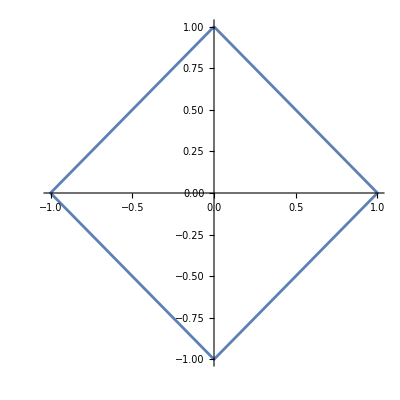

```mathematica
(* draft of a program to draw a square *)

tlist = Range[1,5]; (*establishes a range from 1-4*)
xlist = Cos[π/2 tlist]; (*creates a list of val from tlist multiplied by pi/2 of cos.*)
ylist = Sin[π/2 tlist]; (*creates a list of val from tlist multiplied by pi/2 of sin pts.*)
notSoGoodSquarePts = {xlist, ylist}; (*the pts are not actually coordinates yet*)

squarepts = Transpose[{xlist, ylist}] ;(*this combines the pts from x/y lists into coordinate pairs*)

notSoSquare = ListLinePlot[squarepts] ;(*a squished square is ploted with lines*)

almostFullSquare = ListLinePlot[squarepts, AspectRatio->Automatic] (*this unsquishes it*)
```

## 5. Creating lists with loops

In simulations with Mathematica, we frequently build a list, one element at a time.  We show a few ways to do so.

### Using Append

One way to do so, it to employ the Mathematica function Append, which returns a list with an additional element appended on the end.  The form of a call to the function, where expr is the list and elem is the additional element, follows:  
		Append[expr, elem]

(A template for Append is available in under Classroom Assistant, Basic Commands, List, Lists.)

The segment below returns the value of the list lst with a new element, 5, on the end.  As the output of lst on the last line indicates, however, Append returns the appended list but does not change the original value of lst.

```mathematica
lst = {1, 2, 3, 4};
Append[lst,5]
lst
```

{1,2,3,4,5}

{1,2,3,4}

To have lst be the appended list, we assign the value of the Append function to lst, as follows:

```mathematica
lst = Append[lst,5]
lst
```

{1,2,3,4,5}

{1,2,3,4,5}

The appended element can be a list itself.  In the following example, pts originally represents a list of two points.  After execution, pts contains a third point, the origin.

```mathematica
pts = {{1, 5}, {-2, 7}};
pts = Append[pts, {0, 0}]
```

{{1,5},{-2,7},{0,0}}

In a programming language, such as C, C++ or Java, when using a loop to count, we must initialize the counter to be zero before the loop.  Similarly, we must initialize the first argument of Append to be a list before invocation of Append.  When building a list from scratch, that initial value is usually an empty list, { }. The segment  below defines a function g(x) = 3√x and then stores g(i) for the positive integers i less than 10 in the list gLst, which is originally empty.  Finally, we have Mathematica return the value of gLst.

```mathematica
Clear[g]
g[x_]:=3 √x

gLst = {};
Do[
gLst =  Append[gLst,g[i]],
{i, 9}
]

gLst
```

{3,3 √2,3 √3,6,3 √5,3 √6,3 √7,6 √2,9}

#### QRQ 5.1 Using the comments in the cell below as a guide, write a Mathematica segment to generate a list, lst, of 30 points. Initialize the list to be empty and y to be 1. Inside the body of a Do loop with an integer index i that goes from 0 through 29, make x be 0.25 times i, make y be 1.2 times its previous value, and append the ordered pair of values to the list. After creation of the list of points, plot the points with line segments joining adjacent points and labeled axes. (Notice that the resulting graph is similar to the unconstrained-growth, or exponential, graph in Figure 3.2.2 of Module 3.2 on "Unconstrained Growth and Decay.")

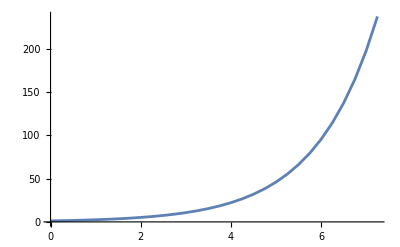

```mathematica
(* initialize list lst to be empty *)
(* initialize y to be 1 *)
(* for i going from 0 through 29 in a loop do the following: *)
(*    assign to x the expression 0.25 times i *)
(*    assign to y the expression 1.2 times previous value of y *)
(*    assign to lst the list, with ordered pair of x and y appended *)
(* plot the points *)

Clear[lst]
lst = {};
y=1;
Do[
x= i*.25;
y= 1.2*y;
lst = Append[lst, {x ,y }], {i,0,29}
]
ListLinePlot[lst,AxesStyle->{"x","y"} ]
```

### Modifying a premade list in a loop

If you know the final length of your list, and that the list is pretty long, it is much more (computing time) efficient to create a list of ones or zeroes of that length, and then replace its elements by the desired values in a loop. Doing so, you’re allocating a memory location in the computer and just changing its value. This is much faster than reallocating memory location at each step, which is what happens with Append. Here is one example:

```mathematica
hlist = Table[0, 10]
Do[hlist[[i]]=2*i+3, {i, 1, 10}]
hlist
```

{0,0,0,0,0,0,0,0,0,0}

{5,7,9,11,13,15,17,19,21,23}

You will learn more about making lists with the powerful command Table in Section 7.

#### QRQ 5.2 Redo QRQ 5.1, using the modifying method above.

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{0.25,1.2},{0.5,1.44},{0.75,1.728},{1.,2.0736},{1.25,2.48832},{1.5,2.98598},{1.75,3.58318},{2.,4.29982},{2.25,5.15978},{2.5,6.19174},{2.75,7.43008},{3.,8.9161},{3.25,10.6993},{3.5,12.8392},{3.75,15.407},{4.,18.4884},{4.25,22.1861},{4.5,26.6233},{4.75,31.948},{5.,38.3376},{5.25,46.0051},{5.5,55.2061},{5.75,66.2474},{6.,79.4968},{6.25,95.3962},{6.5,114.475},{6.75,137.371},{7.,164.845},{7.25,197.814}}

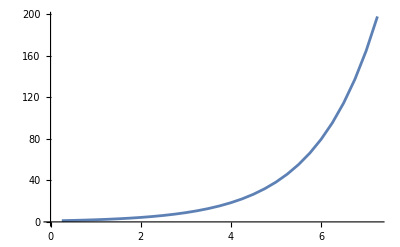

```mathematica
Clear[lst]
lst = Table[0,29];
y=1;
lst
Do[
x= i*.25;
y= 1.2*y;
lst[[i]]= {x ,y }, {i,1,29}
]
lst
ListLinePlot[lst,AxesStyle->{"x","y"} ]
```

## 6. Fitting Data

Let's create some data and plot it:

{{0,1},{1,0},{3,2},{5,4}}

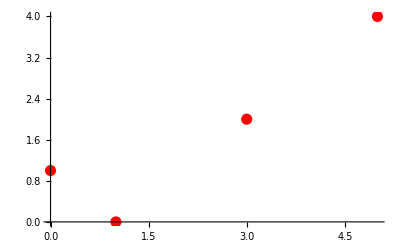

```mathematica
xdata = {0,1,3,5};
ydata = {1,0,2,4};
mydata=Transpose[{xdata, ydata}](* compiles xdata and ydata into a list of points *)
mydataplot = ListPlot[mydata, PlotStyle->{Red, PointSize[.02]}]
```

Here is one of the command you can use to fit a line to this data

```mathematica
Clear[m,b, x]
line = FindFit[mydata,m*x +b, {m,b},x]
```

{m→0.694915,b→0.186441}

(check the command Fit as well). The output is in the annoying form of a replacement rule. We can unpack it:

```mathematica
m/.line
b/.line
m*x+b/.line
```

0.694915

0.186441

0.186441+0.694915 x

where n→3 means “replace n by 3” and "expression/.rule" means : "apply the replacement rule to the expression"

We now graph the data with the line that best fits it (we do the unpacking inside Plot):

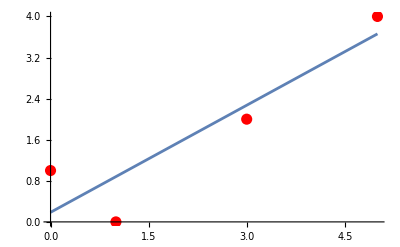

```mathematica
mylinefit =  Plot[m*x+b/.line, {x, 0, 5}];
Show[mydataplot, mylinefit]
```

Note how the command Show is used to combine two graphics.

#### QRQ 6.1. Find the quadratic function that best fits the mydata, and plot the data with the parabola and the line from above.

{a→0.190955,b→-0.266332,c→0.678392}

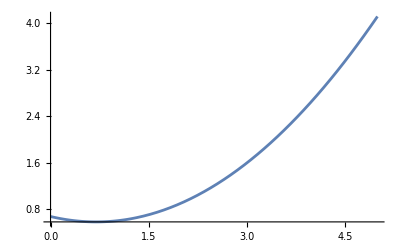

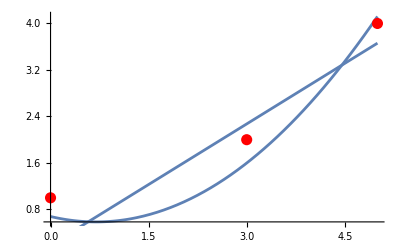

```mathematica
Clear[a,b,c,x]
porabola = FindFit[mydata, a*x^2+b*x+c , {a,b,c},x]
a/.porabola;
b/.porabola;
c/.porabola;
porabfit = Plot[{a x^2+b x+c/.porabola}, {x, 0, 5}]
Show[porabfit,mydataplot,mylinefit]
```

Here is a useful command to produce a common type of list:

```mathematica
Range[3,43]
```

{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43}

### QRQ 6.2. Doubling time of a population of bacteria The population of bacteria in a petri dish is measured every hour (using optical density) and found to be, in 10^8 :

```mathematica
b={1.9, 3.6, 6.9, 13, 25, 47, 85, 140}
```

{1.9,3.6,6.9,13,25,47,85,140}

(Hence, at t = 1 hour, b_1= 1.9 ×10^8, b_2= 3.6 ×10^8...). 
Assuming geometric growth, compute the doubling time, to 2 decimal accuracy.  
Hint. Follow these steps
a.  Use Range to produce the time data and  follow the example of how "squarepts" (QRQ 3.1) was obtained to produce a list {{1, 1.9}, .... ,{8, 140}} of points of time and bacteria population
b. Fit this data to the model B_t= r^t B_0 . The variable is t here, r and B_0 are the parameters to optimize. 
c. Using these values of r and B_0, solve the appropriate equation to find the doubling time.  (Hint. You can do that by hand and with a calculator, but take this opportunity to learn about the Solve function)

```mathematica
Clear[t];
xtime = Range[1,8];
ybac ={1.9, 3.6, 6.9, 13, 25, 47, 85, 140};
pair=Transpose[{xtime, ybac}];
(*fits=FindFit[pair, r^t*bac, {r,bac},{t,1,8}]*)

(*i tried this numerous times, once i recieved the fit, and then it started to provide an error. I am so confused as to why this isnt working but also how to work with this formula is also confusing me.... unfortunately its math i havent touched in years lol*)
```

#### QRQ 6.3 Try to retrace the steps I took during the first class to create a list of the world population from 1800 to 2000 with 20 year steps, and to fit it with an exponential model

## 7. Tables

Another powerful way of creating lists is using the command  Table.  The format is
	Table[expr, {imax}]
	Check these examples, and learn from them:

```mathematica
Table[0, {5}]
Table[2^x, {x,6}]
 Table[i, {i, 1, 16, 3}]
```

{0,0,0,0,0}

{2,4,8,16,32,64}

{1,4,7,10,13,16}

You can make tables of just about anything. Here is  cute example:

```mathematica
Table[Style["text",s],{s,10,20}]
```

{text,text,text,text,text,text,text,text,text,text,text}

Here is a table of points :

```mathematica
tabxsquare = Table[{x,x^2},{x,0,2.5,0.5}]
```

{{0.,0.},{0.5,0.25},{1.,1.},{1.5,2.25},{2.,4.},{2.5,6.25}}

as before these points can be graphed:

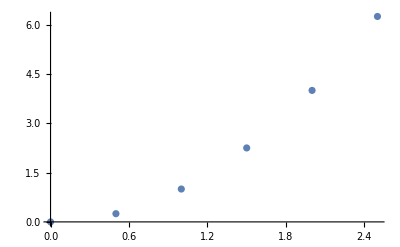

```mathematica
ListPlot[tabxsquare]
```

and displayed in either Matrix, Table, or Grid form (you can add headers):

```mathematica
MatrixForm[tabxsquare]
TableForm[tabxsquare]
Grid[tabxsquare, Frame->All] (* also try Frame -> True *)
Grid[tabxsquare, Frame->True] (* also try Frame -> True *)
Grid[Prepend[tabxsquare, {"carrots", "bananas"}], Frame->All] (* to add headers. Also a good way to add entries on top of a list! *)
```

(0. | 0.
0.5 | 0.25
1. | 1.
1.5 | 2.25
2. | 4.
2.5 | 6.25)

0. | 0.
0.5 | 0.25
1. | 1.
1.5 | 2.25
2. | 4.
2.5 | 6.25

0. | 0.
0.5 | 0.25
1. | 1.
1.5 | 2.25
2. | 4.
2.5 | 6.25

0. | 0.
0.5 | 0.25
1. | 1.
1.5 | 2.25
2. | 4.
2.5 | 6.25

carrots | bananas
0. | 0.
0.5 | 0.25
1. | 1.
1.5 | 2.25
2. | 4.
2.5 | 6.25

Table can be used as a loop, doing the job of the Do and Append at once:

```mathematica
Timing[x=2.0; Table[{i, x=x^2}, {i, 5}]]
```

{0.000023,{{1,4.},{2,16.},{3,256.},{4,65536.},{5,4.29497×10^9}}}

When feasible, this method is often more efficient in Mathematica.

#### QRQ 7.1 a. Create a Do/Append loop that has the same output as the previous command. Which version do you prefer? b. Check out the Timing command and use it to compare the speed of the two computations. You may want to change the range of i a little to get a better sense.

#### c. In QRQ 5.1 above, you generated the following list (lst) of 30 points: {{0, 1.2}, {0.25, 1.44}, {0.5, 1.728}, …, {7.25, 237.376}}. The first coordinate was 0.25 times an index i that varied from 0 to 29. The second coordinate, which was initially 1, was 1.2*(its previous value). Instead of using Do and Append as in QRQ 5.1, first initialize the second coordinate (y) to be 1 and then create the list (lst) by using Table. In the second coordinate, assign y's new value to y.

```mathematica
Clear[x,y, lst]
lst={};
y= 2.0;
Timing[Do[
x=x+1;
y= y^2;
lst= Append[lst,{x,y}], {x,0,4}]]
lst (*i like the table method better. this one is so wasteful of space, and resources. It requires so many things to be written out.*)

(*timing for do append is 0.000033, and timing for table is 0.000023*)

Clear[x,y, lst]
lst = {};
y=1;
Do[
x= i*.25;
y= 1.2*y;
lst = Append[lst, {x ,y }], {i,0,29}
]
lst

Clear[x,y, lst]
y=1; Table[{i* .25, y=1.2*y}, {i,0, 29}]
```

{0.000031,Null}

{{1,4.},{2,16.},{3,256.},{4,65536.},{5,4.29497×10^9}}

{{0.,1.2},{0.25,1.44},{0.5,1.728},{0.75,2.0736},{1.,2.48832},{1.25,2.98598},{1.5,3.58318},{1.75,4.29982},{2.,5.15978},{2.25,6.19174},{2.5,7.43008},{2.75,8.9161},{3.,10.6993},{3.25,12.8392},{3.5,15.407},{3.75,18.4884},{4.,22.1861},{4.25,26.6233},{4.5,31.948},{4.75,38.3376},{5.,46.0051},{5.25,55.2061},{5.5,66.2474},{5.75,79.4968},{6.,95.3962},{6.25,114.475},{6.5,137.371},{6.75,164.845},{7.,197.814},{7.25,237.376}}

{{0.,1.2},{0.25,1.44},{0.5,1.728},{0.75,2.0736},{1.,2.48832},{1.25,2.98598},{1.5,3.58318},{1.75,4.29982},{2.,5.15978},{2.25,6.19174},{2.5,7.43008},{2.75,8.9161},{3.,10.6993},{3.25,12.8392},{3.5,15.407},{3.75,18.4884},{4.,22.1861},{4.25,26.6233},{4.5,31.948},{4.75,38.3376},{5.,46.0051},{5.25,55.2061},{5.5,66.2474},{5.75,79.4968},{6.,95.3962},{6.25,114.475},{6.5,137.371},{6.75,164.845},{7.,197.814},{7.25,237.376}}

## 8.Tables and graphics

Mathematica has a bank of 2D "graphics primitives". You can access a list of them, and many other graphing tools, at Palettes, Classroom Assistant, Basic Commands, 2D 
Here is one example:



```mathematica
Graphics[Circle[{1,0},1/2]]
```

#### QRQ 8.1. a. Use the Classroom Assistant Basic Commands, 2D, to show the axes, and make the origin of the axes = (0, 0) in the previous Graphics command to see that the circle is the one you think it is.

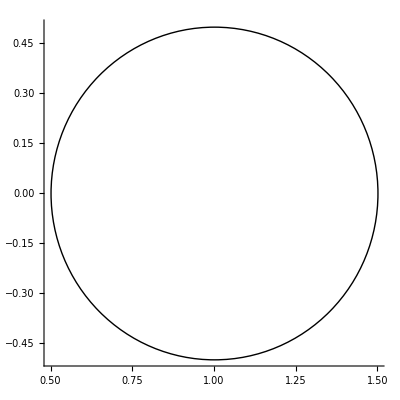

```mathematica
Graphics[Circle[{1,0},1/2],{Axes->True}, AxesOrigin->{0,0}]
```

#### b. Use a Graphics primitive to draw a square centered at (1,0), of side 1. Why is this command not interchangeable with the program you used to draw a square earlier?

#### Using Tables with graphics

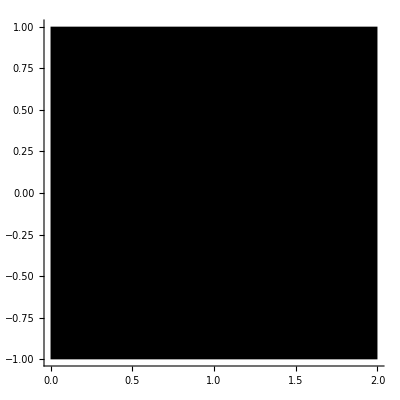

```mathematica
Graphics[Rectangle[{0,-1},{2,1}],{Axes->True}]
(*this one isnt opaque its solid, this you also cannot change as easily, there are only two points isntead of connecting all corners.*)
```

You can use tables to make repeated graphics. The object in the following table are "graphics primitive" :

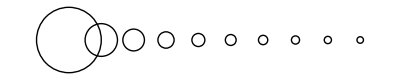

```mathematica
circles = Table[Graphics[Circle[{i,0},1/i]], {i, 1, 10}]; (* name your graphics to use later *)
Show[circles] (* this Show command enables to see several graphics at their respective places *)
```

A fancier version, using some Graphics Directives such as Thickness, RGBColor... (for more, see Classroom Assistant, Basic Commands, 2D, Directives , below Graphics.

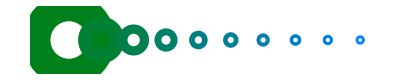

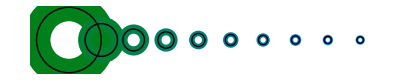

```mathematica
fancyCircles =
 Table[
Graphics[
{Thickness[0.05/i],RGBColor[0,.5 , i/10],(* RGB: Red, Green, Blue *)
Circle[{i,0},1/i]}], 
{i, 1, 10}];
Show[fancyCircles]
Show[fancyCircles, circles]
```

#### QRQ 8.2 Show the previous collection of circles with their center points in yellow

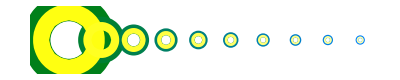

```mathematica
circles = Table[
Graphics[
{Thickness[.1/i],RGBColor[1,1 , i/15],Circle[{i,0},.25/i]}], {i, 1, 10}
];
Show[fancyCircles,circles]
```

#### QRQ 8.3 Go to town, be creative and make a beautiful picture using Graphics, Primitives, Directives and Table. You can even include some text, and put some Manipulate in the mix!

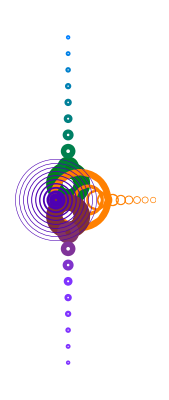

```mathematica
circless = Table[
Graphics[
{Thickness[.1/i ],RGBColor[1,.5, 0 ],Circle[{i*2,0},.8/i]}], {i, 1, 10}
];
circlestwo = Table[
Graphics[
{Thickness[.01/i ],RGBColor[.3,0, .7 ],Circle[{-4,0},i]}], {i, 1, 10}
];
fancyCircless =
 Table[
Graphics[
{Thickness[0.05/i],RGBColor[0,.5 , i/10],(* RGB: Red, Green, Blue *)
Circle[{-1,i*4},2/i]}], 
{i, 1, 10}];
fancyCirclestwo =
 Table[
Graphics[
{Thickness[0.05/i],RGBColor[.5,.2 , i*.2],(* RGB: Red, Green, Blue *)
Circle[{-1,-i*4},2/i]}], 
{i, 1, 10}];
Show[fancyCircless,circless, fancyCirclestwo, circlestwo]
```